```mathematica
n=5;
k=0;
h=0.1;
α=1+0.4*k;
β=1+0.4*n;
Subscript[x, 0]=0;
Subscript[y, 0]=0;
y'[x_,y_]:=α/(x^2+y^2+β);
Do[Subscript[x, i+1]=Subscript[x, i]+h,{i,0,10}];
```

## Метод Рунге-Кутты

```mathematica
For[i=0,i<12,i++,
Subscript[k, 1]=h*y'[Subscript[x, i],Subscript[y, i]];
Subscript[k, 2]=h*y'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k, 1]/2];
Subscript[k, 3]=h*y'[Subscript[x, i]+h/2,Subscript[y, i]+Subscript[k, 2]/2];
Subscript[k, 4]=h*y'[Subscript[x, i]+h,Subscript[y, i]+Subscript[k, 3]];
Subscript[y, i+1]=Subscript[y, i]+1/6(Subscript[k, 1]+2*Subscript[k, 2]+2*Subscript[k, 3]+Subscript[k, 4]);
];
```

```mathematica
Table[Subscript[y, i],{i,0,12}]
```

{0,0.0332923,0.0663405,0.098912,0.130795,0.161807,0.191798,0.220654,0.248295,0.274672,0.299766,0.323578,0.346129}

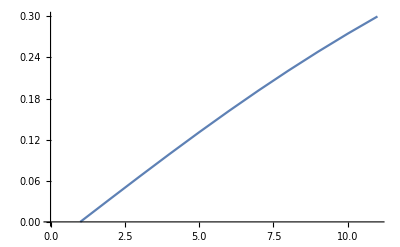

```mathematica
ListPlot[Table[Subscript[y, i],{i,0,10}],Joined->True]
```

# Экстраполяционный метод

```mathematica
(*
q - это базовый случай, следующие значения считаются на 5 шагов вперёд
*)
q=7;
Subscript[y, q+1]=Subscript[y, q]+h*y'[Subscript[x, q],Subscript[y, q]];
Subscript[y, q+2]=Subscript[y, q+1]+h*(3/2 y'[Subscript[x, q+1],Subscript[y, q+1]]-1/2 y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+3]=Subscript[y, q+2]+h*(23/12 y'[Subscript[x, q+2],Subscript[y, q+2]]-4/3 y'[Subscript[x, q+1],Subscript[y, q+1]]+5/12 y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+4]=Subscript[y, q+3]+h(55/24*y'[Subscript[x, q+3],Subscript[y, q+3]]-59/24*y'[Subscript[x, q+2],Subscript[y, q+2]]+37/24*y'[Subscript[x, q+1],Subscript[y, q+1]]-3/8*y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+5]=Subscript[y, q+4]+h(1901/720*y'[Subscript[x, q+4],Subscript[y, q+4]]-1387/360*y'[Subscript[x, q+3],Subscript[y, q+3]]+109/30*y'[Subscript[x, q+2],Subscript[y, q+2]]-637/360*y'[Subscript[x, q+1],Subscript[y, q+1]]+251/720*y'[Subscript[x, q],Subscript[y, q]]);
Table[Subscript[y, i],{i,0,12}]
```

{0,0.0332923,0.0663405,0.098912,0.130795,0.161807,0.191798,0.220654,0.248913,0.275302,0.300385,0.324196,0.346745}

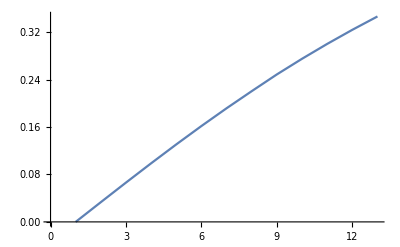

```mathematica
ListPlot[Table[Subscript[y, i],{i,0,12}],Joined->True]
```

## Интерполяционный метод

```mathematica
(*
q - это базовый случай, следующие значения считаются на 5 шагов вперёд
*)
q=7;
Subscript[y, q+1]=Subscript[y, q]+h*y'[Subscript[x, q],Subscript[y, q]];
Subscript[y, q+2]=Subscript[y, q+1]+1/2*h(y'[Subscript[x, q+1],Subscript[y, q+1]]+y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+3]=Subscript[y, q+2]+h(5/12*y'[Subscript[x, q+2],Subscript[y, q+2]]+2/3*y'[Subscript[x, q+1],Subscript[y, q+1]]-1/12*y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+4]=Subscript[y, q+3]+h(3/8*y'[Subscript[x, q+3],Subscript[y, q+3]]+19/24*y'[Subscript[x, q+2],Subscript[y, q+2]]-5/24*y'[Subscript[x, q+1],Subscript[y, q+1]]+1/24*y'[Subscript[x, q],Subscript[y, q]]);
Subscript[y, q+5]=Subscript[y, q+4]+h(251/720*y'[Subscript[x, q+4],Subscript[y, q+4]]+646/720*y'[Subscript[x, q+3],Subscript[y, q+3]]-264/720*y'[Subscript[x, q+2],Subscript[y, q+2]]+106/720*y'[Subscript[x, q+1],Subscript[y, q+1]]-19/720*y'[Subscript[x, q],Subscript[y, q]]);
```

```mathematica
Table[Subscript[y, i],{i,0,12}]
```

{0,0.0332923,0.0663405,0.098912,0.130795,0.161807,0.191798,0.220654,0.248913,0.276549,0.302923,0.328007,0.351806}

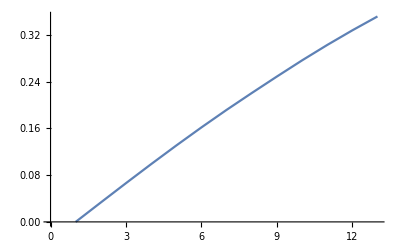

```mathematica
ListPlot[Table[Subscript[y, i],{i,0,12}],Joined->True]
```